# Initialize:

## STE calculations:

```mathematica
Symbolize[array_?ArrayQ, m_?IntegerQ]:= Module[
{symbols, orderedtriplets, symbarray},
symbols = Permutations[Range[1,m]];
orderedtriplets = Table[Sort[{Range[1,m], array⟦Range[i,i+(m-1)]⟧}ᵀ,#1⟦2⟧<#2⟦2⟧&]⟦All,1⟧,{i,1,Length[array]-(m-1)}];
symbarray = ReplacePart[orderedtriplets, Flatten[Table[Rule[#,i]&/@Flatten[Position[orderedtriplets, symbols⟦i⟧]],{i,m!}]]];
Return[symbarray]
]
```

```mathematica
STEcalc[xmat_?ArrayQ, ymat_?ArrayQ, m_?IntegerQ]:= Module[{symbols, xsymbmat, ysymbmat, to, possibleTransitions, triplets,loopset,TE},

(*--- Symbolize the arrays ---*)
symbols = Permutations[Range[1,m]];
xsymbmat = Symbolize[#,m]&/@xmat;
ysymbmat = Symbolize[#,m]&/@ymat;

(*--- Calculate the possible symbol-to-symbol transitions ---*)
to = Table[Drop[symbols⟦i⟧, Flatten[Position[symbols⟦i⟧,m]]],{i,1,Length[symbols]}];
possibleTransitions = Table[
Flatten[Position[to,(Drop[symbols⟦s⟧, Flatten[Position[symbols⟦s⟧,1]]]-1)]] 
,{s,1,Length[symbols]}];

(*--- Calculate the symbolic transfer entropy ---*)
triplets = Partition[Flatten[Table[
{Reverse[Partition[xsymbmat⟦i⟧,2,1],{2}], Drop[ysymbmat⟦i⟧,-1]}ᵀ
,{i,Length[xsymbmat]}]],3];
loopset = Partition[Flatten[Table[Table[{#,i,j}&/@possibleTransitions⟦i⟧,{i,Length[possibleTransitions]}],{j,1,m!}]],3];
TE = Total[(1/Length[triplets])*Table[Count[triplets, set]* Log[2,(Count[triplets, set]/Count[triplets⟦All,{2,3}⟧,set⟦{2,3}⟧])/(Count[triplets⟦All,{1,2}⟧, set⟦{1,2}⟧]/Count[triplets⟦All,2⟧, set⟦2⟧])],{set,loopset}]];
Return[N[TE]];
]
```

## The SIR simulator:

S0: vector of initial susceptible (default {499,  500})
I0: vector of initial infected (default {1, 0})
β: matrix of cross-class infection rates 
γ: scalar recovery rate 
maxits: maximum number of Gillespie iterations to run 
maxt: maximum number of weeks to cap output

```mathematica
SIRGillespieAgeMaxt[S0_,I0_,β_,γ_,maxits_,maxt_] := Module[{nclass,NN, SS, II,t,SSTransitions, IITransitions, infrates, recrates, totrate, τ,ratelist, cumratelist, draw, event, SSnew, IInew},
If[Length[S0]≠ Length[I0], Print["Error"]; Return[]]; (*the vectors don't have the same length, and so don't specify the same number of age classes; the simulation can't continue*)
nclass = Length[S0]; (*specify the number of age classes there are*)
NN = Total[S0] + Total[I0]; (*calculate the total population size*)
SS = {S0}; (*initialize an array of susceptible counts*)
II = {I0}; (*initialize an array of infected counts*)
t = {0}; (*initialize an array to store time points*)
SSTransitions = Join[DiagonalMatrix[ConstantArray[-1, nclass]],ConstantArray[ConstantArray[0,nclass],nclass]];
IITransitions = Join[DiagonalMatrix[ConstantArray[1, nclass]],DiagonalMatrix[ConstantArray[-1, nclass]]];
Do[
infrates = 1/NN*DiagonalMatrix[SS⟦it⟧].β.II⟦it⟧;
recrates = γ*II⟦it⟧;
totrate = Total[infrates] + Total[recrates];

(*Calculate the time to next transition*)
If[totrate==0, 
Return[{SS, II,t}], 
τ = RandomVariate[ExponentialDistribution[totrate]];
];

(*Identify the transition*)
ratelist = Join[infrates, recrates]/totrate;
cumratelist = Table[Total[ratelist⟦Range[1,i]⟧],{i,Length[ratelist]}];
draw = RandomVariate[UniformDistribution[]]; 
event = Flatten[Position[cumratelist, _?(#>draw&)]]⟦1⟧;
SSnew = SS⟦it⟧ + SSTransitions⟦event⟧;
IInew = II⟦it⟧ + IITransitions⟦event⟧;
SS = Join[SS, {SSnew}];
II = Join[II, {IInew}];
t = Join[t,{t⟦it⟧+τ}];
If[t⟦it⟧+τ > maxt, Return[{SS, II,t}]];
,{it, maxits}];
Return[{SS, II,t}];
]
```

## The Poisson simulator:

```mathematica
RPoisson[μ_] := If[μ>0, RandomVariate[PoissonDistribution[μ]],0];
```

```mathematica
PoissonSim[initinf_, genlength_, epilength_, changepoint_, NGMHigh_, NGMLow_, gensperbin_]:=Module[{ngens, ivec, binvec},
(* calculate how many generations are in the outbreak: *)
ngens = Ceiling[epilength/genlength];
(* initialize vector of infecteds: *)
ivec = {initinf};
(* run the simulation *)
Table[ivec = Join[ivec, 
If[it*genlength≤changepoint, (*if we're before the changepoint,*)
{RPoisson/@(NGMHigh.ivec⟦-1⟧)}, (*iterate using NGMHigh x previous infected*)
{RPoisson/@(NGMLow.ivec⟦-1⟧)} (*else, iterate using NGMLow x previous infected*)
]
],{it, ngens}];
binvec = Total/@Partition[ivec,gensperbin]; (*bin the observed infections*)
Return[binvec];
]
```

# SIR Z/K Plots:

## For Z:

```mathematica
zrange = Range[0,1,0.1];
TEmatFull = {};
Do[
R0 = 1.5;  (*fix an R0 from the start, to ensure interpretability/cross-comparability of results - confusingly, this is not the intial recovered, but the basic reproduction number*)
γ = N[1/7]; (*recovery rate*)
maxits = 5000; (*max number of iterations to run each Gillespie simulation*)
nepidemics = 800; (*fix the number of (successful) outbreaks to run, for each TE calculation, default 800*)
ntecalcs = 100; (*number of ensembles to run; this is the number of TE estimates we'll get, from which we'll generate a distribution, defualt 100*)
binwidth = 7; (*number of days to bin gillespie output into (7 = weekly bins, 3.5 = half-weekly bins)*)
noisefraction = .005; (*what fraction of the pop size gets random respiratory illness each week*)
maxt = 175; (*longest time to run the epidemic for*)
pvec ={0.5, 0.5}; (*vector of the fractional percentages of the population made up by each age group*)
nclasses = 2;
β = (γ R0)/(1+z)*DiagonalMatrix[1/pvec].{{1,z},{z,1}}; (*the transmission matrix*)
ngm = 1/γ*DiagonalMatrix[pvec].β; (*calculate the next generation matrix from the elements defined above*)
TEmat = {}; (*initialize a vector to store the transfer entropy matrices in*)
DistributeDefinitions[SIRGillespieAgeMaxt];
DistributeDefinitions[STEcalc];
DistributeDefinitions[zrange];
DistributeDefinitions[nclasses];
DistributeDefinitions[β];
DistributeDefinitions[γ];
DistributeDefinitions[maxits];
DistributeDefinitions[nepidemics];
DistributeDefinitions[ntecalcs];
DistributeDefinitions[ntecalcs];
DistributeDefinitions[binwidth];
DistributeDefinitions[noisefraction];
DistributeDefinitions[maxt];
SetSharedVariable[TEmat];
ParallelDo[
IImat = ConstantArray[0,{nclasses,nepidemics,Floor[maxt/binwidth]}];
successes = 0; (*initialize a variable to store how many epidemics have taken off*)
While[successes < nepidemics,
draw = RandomReal[];
If[draw>0.5, I0 = {1,0};S0 = {499,500},(*else*) I0 = {0,1}; S0 = {500,499}];
{SS, II,t} = SIRGillespieAgeMaxt[S0,I0,β,γ,maxits, maxt];
ncases = Total[Table[Count[Drop[II⟦All,c⟧,1] - Drop[II⟦All,c⟧,-1] ,_?(#>0&)],{c, nclasses}]];
If[ncases>100, (*if the epidemic has proceeded for sufficient time*)
successes = successes + 1;
binindices = Table[
Flatten[Position[t,_?(#≥i*binwidth && #<(i+1)*binwidth&)]],{i,0,Ceiling[(maxt-binwidth)/binwidth](*Ceiling[Max[t]/binwidth]*)}];
noise = Table[Table[RandomVariate[PoissonDistribution[noisefraction*(S0⟦i⟧+I0⟦i⟧)]],{i,nclasses}],{Length[binindices]}];
binnedinfections = Table[
If[Length[SS⟦binindices⟦i⟧⟧]>0,
SS⟦binindices⟦i⟧⟧⟦1⟧ - SS⟦binindices⟦i⟧⟧⟦-1⟧,
ConstantArray[0,Length[SS⟦1⟧]]]
,{i,Length[binindices]}] + noise;
Do[
IImat⟦i,successes⟧ = binnedinfections⟦Range[1,Floor[maxt/binwidth]],i⟧;
,{i,nclasses}]
];
];
te = Table[Table[If[i≠j,STEcalc[IImat⟦j⟧, IImat⟦i⟧,3],0],{i,nclasses}],{j,nclasses}];
TEmat = Join[TEmat, {te}];
,{teind,1,ntecalcs}];
TEmatFull = Join[TEmatFull, {TEmat}];
Print[z];
,{z,zrange}];
```

0.

0.1

0.2

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1.

```mathematica
TEmatZ = TEmatFull;
```

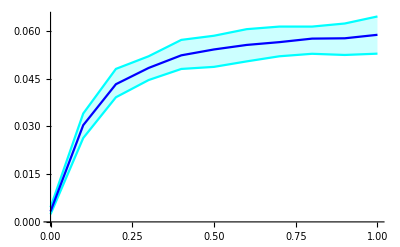

```mathematica
chplotQuantile = ListLinePlot[
{
Table[{zrange⟦i⟧, Quantile[TEmatZ⟦i,All,2,1⟧,0.05]},{i,Length[TEmatZ]}],
Table[{zrange⟦i⟧, Quantile[TEmatZ⟦i,All,2,1⟧,0.95]},{i,Length[TEmatZ]}],
Table[{zrange⟦i⟧, Mean[TEmatZ⟦i,All,2,1⟧]},{i,Length[TEmatZ]}]
},
PlotStyle->{Cyan, Cyan, Blue},
Filling->{1->{2}}
]
```

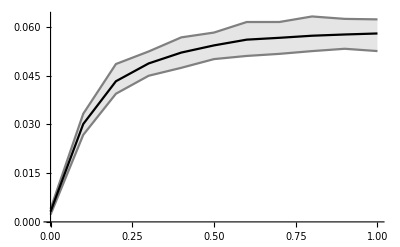

```mathematica
adplotQuantile = ListLinePlot[
{
Table[{zrange⟦i⟧, Quantile[TEmatZ⟦i,All,1,2⟧,0.05]},{i,Length[TEmatZ]}],
Table[{zrange⟦i⟧, Quantile[TEmatZ⟦i,All,1,2⟧,0.95]},{i,Length[TEmatZ]}],
Table[{zrange⟦i⟧, Mean[TEmatZ⟦i,All,1,2⟧]},{i,Length[TEmatZ]}]
},
PlotStyle->{Gray, Gray, Black},
Filling->{1->{2}}
]
```

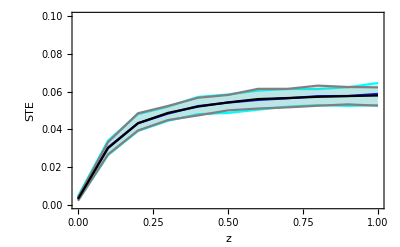

```mathematica
zquantileplot = Show[chplotQuantile, adplotQuantile,
PlotRange->{0,0.1}, 
Frame->{True,True,False,False}, 
Axes->None,
FrameLabel->{"z","STE"},
BaseStyle->{FontSize->14},
ImageSize->400]
```

## For K:

```mathematica
krange = Range[0,1,0.1];
TEmatFull = {};
Do[
R0 = 1.5;  (*fix an R0 from the start, to ensure interpretability/cross-comparability of results - confusingly, this is not the intial recovered, but the basic reproduction number*)
γ = N[1/7]; (*recovery rate*)
maxits = 5000; (*max number of iterations to run each Gillespie simulation*)
nepidemics = 800; (*fix the number of (successful) outbreaks to run, for each TE calculation, default 800*)
ntecalcs = 100; (*number of ensembles to run; this is the number of TE estimates we'll get, from which we'll generate a distribution, defualt 100*)
binwidth = 7; (*number of days to bin gillespie output into (7 = weekly bins, 3.5 = half-weekly bins)*)
noisefraction = .005; (*what fraction of the pop size gets random respiratory illness each week*)
maxt = 175; (*longest time to run the epidemic for*)
pvec = {0.5, 0.5}; (*vector of the fractional percentages of the population made up by each age group*)
nclasses = 2;
β = (2 γ R0)/(2 + 3 k + √(9 k^2 + 4 k + 4))*DiagonalMatrix[1/pvec].{{1+3 k,1},{1 + k,1}}; (*the transmission matrix*)
ngm = 1/γ*DiagonalMatrix[pvec].β; (*calculate the next generation matrix from the elements defined above*)
TEmat = {}; (*initialize a vector to store the transfer entropy matrices in*)
DistributeDefinitions[SIRGillespieAgeMaxt];
DistributeDefinitions[STEcalc];
DistributeDefinitions[krange];
DistributeDefinitions[nclasses];
DistributeDefinitions[β];
DistributeDefinitions[γ];
DistributeDefinitions[maxits];
DistributeDefinitions[nepidemics];
DistributeDefinitions[ntecalcs];
DistributeDefinitions[ntecalcs];
DistributeDefinitions[binwidth];
DistributeDefinitions[noisefraction];
DistributeDefinitions[maxt];
SetSharedVariable[TEmat];
ParallelDo[
IImat = ConstantArray[0,{nclasses,nepidemics,Floor[maxt/binwidth]}];
successes = 0; (*initialize a variable to store how many epidemics have taken off*)
While[successes < nepidemics,
draw = RandomReal[];
If[draw>0.5, I0 = {1,0};S0 = {499,500},(*else*) I0 = {0,1}; S0 = {500,499}];
{SS, II,t} = SIRGillespieAgeMaxt[S0,I0,β,γ,maxits, maxt];
ncases = Total[Table[Count[Drop[II⟦All,c⟧,1] - Drop[II⟦All,c⟧,-1] ,_?(#>0&)],{c, nclasses}]];
If[ncases>100, (*if the epidemic has proceeded for sufficient time*)
successes = successes + 1;
binindices = Table[
Flatten[Position[t,_?(#≥i*binwidth && #<(i+1)*binwidth&)]],{i,0,Ceiling[(maxt-binwidth)/binwidth](*Ceiling[Max[t]/binwidth]*)}];
noise = Table[Table[RandomVariate[PoissonDistribution[noisefraction*(S0⟦i⟧+I0⟦i⟧)]],{i,nclasses}],{Length[binindices]}];
binnedinfections = Table[
If[Length[SS⟦binindices⟦i⟧⟧]>0,
SS⟦binindices⟦i⟧⟧⟦1⟧ - SS⟦binindices⟦i⟧⟧⟦-1⟧,
ConstantArray[0,Length[SS⟦1⟧]]]
,{i,Length[binindices]}] + noise;
Do[
IImat⟦i,successes⟧ = binnedinfections⟦Range[1,Floor[maxt/binwidth]],i⟧;
,{i,nclasses}]
];
];
te = Table[Table[If[i≠j,STEcalc[IImat⟦j⟧, IImat⟦i⟧,3],0],{i,nclasses}],{j,nclasses}];
TEmat = Join[TEmat, {te}];
,{teind,1,ntecalcs}];
TEmatFull = Join[TEmatFull, {TEmat}];
Print[k];
,{k,krange}];
```

0.

0.1

0.2

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1.

```mathematica
TEmatK = TEmatFull;
```

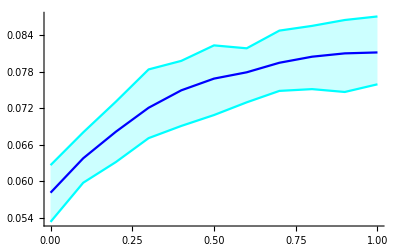

```mathematica
chplotQuantile = ListLinePlot[
{
Table[{krange⟦i⟧, Quantile[TEmatK⟦i,All,2,1⟧,0.05]},{i,Length[TEmatK]}],
Table[{krange⟦i⟧, Quantile[TEmatK⟦i,All,2,1⟧,0.95]},{i,Length[TEmatK]}],
Table[{krange⟦i⟧, Mean[TEmatK⟦i,All,2,1⟧]},{i,Length[TEmatK]}]
},
PlotStyle->{Cyan, Cyan, Blue},
Filling->{1->{2}}
]
```

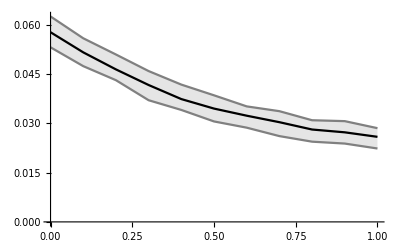

```mathematica
adplotQuantile = ListLinePlot[
{
Table[{krange⟦i⟧, Quantile[TEmatK⟦i,All,1,2⟧,0.05]},{i,Length[TEmatK]}],
Table[{krange⟦i⟧, Quantile[TEmatK⟦i,All,1,2⟧,0.95]},{i,Length[TEmatK]}],
Table[{krange⟦i⟧, Mean[TEmatK⟦i,All,1,2⟧]},{i,Length[TEmatK]}]
},
PlotStyle->{Gray, Gray, Black},
Filling->{1->{2}}
]
```

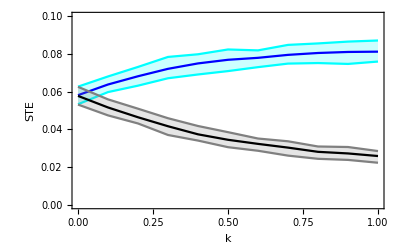

```mathematica
kquantileplot = Show[chplotQuantile, adplotQuantile,
PlotRange->{0,0.1}, 
Frame->{True,True,False,False}, 
Axes->None,
FrameLabel->{"k","STE"},
BaseStyle->{FontSize->14},
ImageSize->400]
```

# Poisson Z/K Plots:

## For Z:

```mathematica
zrange = Range[0,1,0.1];
TEmatFull = ConstantArray[{},Length[zrange]];
SetSharedVariable[TEmatFull];
DistributeDefinitions[Symbolize];
DistributeDefinitions[STEcalc];
DistributeDefinitions[zrange];
ParallelDo[
nTEits = 100;
TEmat = {};
RHigh = 1.5;
RLow =0.8;
Do[
(* INITIALIZE VALUES *)
ivecfull = {};
NGMstruct={{1,zrange⟦ngmadj⟧},{zrange⟦ngmadj⟧,1}};
NGMHigh = RHigh*N[NGMstruct / Max[Eigenvalues[NGMstruct]]];
NGMLow = RLow*N[NGMstruct / Max[Eigenvalues[NGMstruct]]];
changepoint = 28; (*number of generation intervals after which to switch to the RLow*)
epilength = 175; (*length of epidemic in days*)
gensperbin = 2; (*number of generations per bin*)
genlength = 3.5; (*length of generation interval in days*)
noiserate =10; (*amount of noise to inject into each category, in each bin*)
nepidemics = 800; (*number of epidemics per STE calculation*)

(* RUN THE EPIDEMIC SIMULATION *)
While[Length[ivecfull]< nepidemics,
draw = RandomReal[];
If[draw>0.5, initinf = {1,0}, initinf = {0,1} ];
ivec = PoissonSim[initinf, genlength, epilength, changepoint, NGMHigh, NGMLow,gensperbin];
If[Total[Flatten[ivec]]>100, 
ivecnoisy = ivec +  RandomVariate[PoissonDistribution[noiserate], {Length[ivec],Length[NGMHigh]}];
ivecfull = Join[ivecfull, {ivecnoisy}]
];
];

(* CALCULATE THE STE *)
TEmat = Join[TEmat, {Table[Table[
If[i==j,0,STEcalc[ivecfull⟦All,All,j⟧, ivecfull⟦All,All,i⟧, 3]]
,{i,1,Length[NGMHigh]}],{j,1,Length[NGMHigh]}]}];
,{indexA, nTEits}];
TEmatFull⟦ngmadj⟧ = TEmat;

Print[ngmadj];
,{ngmadj,1,Length[zrange]}];
TEmatFullZ = TEmatFull;
```

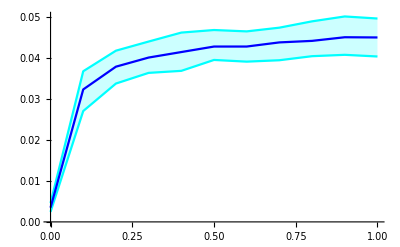

```mathematica
chplotQuantileZ = ListLinePlot[
{
Table[{zrange⟦i⟧, Quantile[TEmatFullZ⟦i,All,2,1⟧,0.05]},{i,Length[TEmatFullZ]}],
Table[{zrange⟦i⟧, Quantile[TEmatFullZ⟦i,All,2,1⟧,0.95]},{i,Length[TEmatFullZ]}],
Table[{zrange⟦i⟧, Mean[TEmatFullZ⟦i,All,2,1⟧]},{i,Length[TEmatFullZ]}]
},
PlotStyle->{Cyan, Cyan, Blue},
Filling->{1->{2}}
]
```

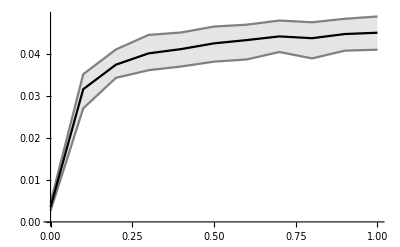

```mathematica
adplotQuantileZ = ListLinePlot[
{
Table[{zrange⟦i⟧, Quantile[TEmatFullZ⟦i,All,1,2⟧,0.05]},{i,Length[TEmatFullZ]}],
Table[{zrange⟦i⟧, Quantile[TEmatFullZ⟦i,All,1,2⟧,0.95]},{i,Length[TEmatFullZ]}],
Table[{zrange⟦i⟧, Mean[TEmatFullZ⟦i,All,1,2⟧]},{i,Length[TEmatFullZ]}]
},
PlotStyle->{Gray, Gray, Black},
Filling->{1->{2}}
]
```

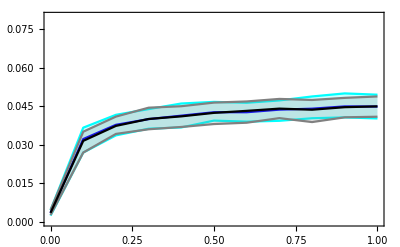

```mathematica
zplot = Show[chplotQuantileZ, adplotQuantileZ, PlotRange->{0, 0.08}, Frame->True, Axes->None]
```

## For K:

```mathematica
Export["~/Desktop/startedk.txt", "Started K at "<>DateString[]];
krange = Range[0,1,0.1];
TEmatFull = ConstantArray[{},Length[krange]];
SetSharedVariable[TEmatFull];
DistributeDefinitions[Symbolize];
DistributeDefinitions[STEcalc];
DistributeDefinitions[krange];
ParallelDo[
nTEits = 100;
TEmat = {};
RHigh = 1.5;
RLow =0.8;
Do[
(* INITIALIZE VALUES *)
ivecfull = {};
NGMstruct = {{1+3*krange⟦ngmadj⟧,1},{1+krange⟦ngmadj⟧,1}};
NGMHigh = RHigh*N[NGMstruct / Max[Eigenvalues[NGMstruct]]];
NGMLow = RLow*N[NGMstruct / Max[Eigenvalues[NGMstruct]]];
changepoint = 28; (*number of generation intervals after which to switch to the RLow*)
epilength = 175; (*length of epidemic in days*)
gensperbin = 2; (*number of generations per bin*)
genlength = 3.5;  (*length of generation interval in days*)
noiserate =10; (*amount of noise to inject into each category, in each bin*)
nepidemics = 800;(*number of epidemics per STE calculation*)

(* RUN THE EPIDEMIC SIMULATION *)
While[Length[ivecfull]< nepidemics,
draw = RandomReal[];
If[draw>0.5, initinf = {1,0}, initinf = {0,1} ];
ivec = PoissonSim[initinf, genlength, epilength, changepoint, NGMHigh, NGMLow,gensperbin];
If[Total[Flatten[ivec]]>100, 
ivecnoisy = ivec +  RandomVariate[PoissonDistribution[noiserate], {Length[ivec],Length[NGMHigh]}];
ivecfull = Join[ivecfull, {ivecnoisy}]
];
];

(* CALCULATE THE STE *)
TEmat = Join[TEmat, {Table[Table[
If[i==j,0,STEcalc[ivecfull⟦All,All,j⟧, ivecfull⟦All,All,i⟧, 3]]
,{i,1,Length[NGMHigh]}],{j,1,Length[NGMHigh]}]}];
,{indexA, nTEits}];
TEmatFull⟦ngmadj⟧ = TEmat;

Print[ngmadj];
,{ngmadj,1,Length[krange]}];
TEmatFullK = TEmatFull;
```

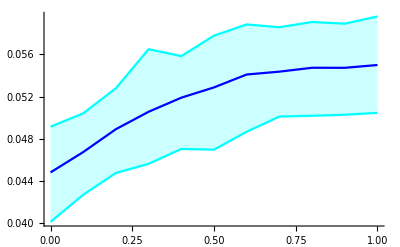

```mathematica
chplotQuantileK = ListLinePlot[
{
Table[{krange⟦i⟧, Quantile[TEmatFullK⟦i,All,2,1⟧,0.05]},{i,Length[TEmatFullK]}],
Table[{krange⟦i⟧, Quantile[TEmatFullK⟦i,All,2,1⟧,0.95]},{i,Length[TEmatFullK]}],
Table[{krange⟦i⟧, Mean[TEmatFullK⟦i,All,2,1⟧]},{i,Length[TEmatFullK]}]
},
PlotStyle->{Cyan, Cyan, Blue},
Filling->{1->{2}}
]
```

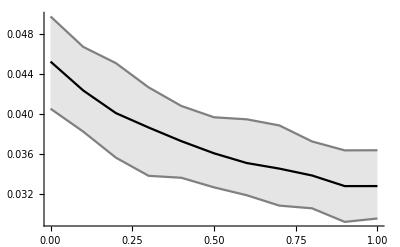

```mathematica
adplotQuantileK = ListLinePlot[
{
Table[{krange⟦i⟧, Quantile[TEmatFullK⟦i,All,1,2⟧,0.05]},{i,Length[TEmatFullK]}],
Table[{krange⟦i⟧, Quantile[TEmatFullK⟦i,All,1,2⟧,0.95]},{i,Length[TEmatFullK]}],
Table[{krange⟦i⟧, Mean[TEmatFullK⟦i,All,1,2⟧]},{i,Length[TEmatFullK]}]
},
PlotStyle->{Gray, Gray, Black},
Filling->{1->{2}}
]
```

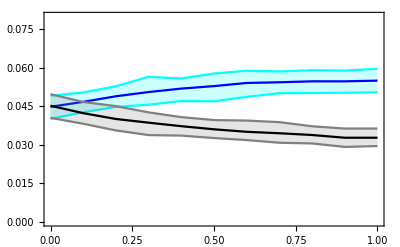

```mathematica
kplot = Show[chplotQuantileK, adplotQuantileK, PlotRange->{0, 0.08}, Frame->True, Axes->None]
```

## Together:

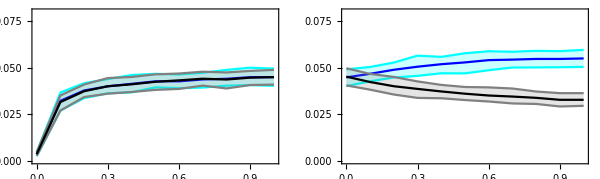

```mathematica
GraphicsGrid[{{zplot, kplot}}, ImageSize->600]
```

# 4-age-class Poisson model with varying reporting rate

## The simulation:

Simulate 100 ensembles:

```mathematica
nensembles = 100; 
RHigh = 1.5;
RLow =0.8;
NGMstruct = {
{1,2,1,1},
{1,4,1,1},
{1,2,1,1},
{1,1,1,1}
};
NGMHigh = RHigh*N[NGMstruct / Max[Eigenvalues[NGMstruct]]];
NGMLow = RLow*N[NGMstruct / Max[Eigenvalues[NGMstruct]]];
changepoint = 28; 
epilength = 175;
gensperbin = 2;
genlength = 3.5; 
noiserate =10; 
nepidemics = 800;

minncases = 400(*4500*);
ivecAllEnsembles = ConstantArray[{},nensembles];

SetSharedVariable[ivecAllEnsembles];
DistributeDefinitions[RHigh];
DistributeDefinitions[RLow];
DistributeDefinitions[NGMstruct];
DistributeDefinitions[NGMHigh];
DistributeDefinitions[NGMLow];
DistributeDefinitions[changepoint];
DistributeDefinitions[epilength];
DistributeDefinitions[gensperbin];
DistributeDefinitions[genlength];
DistributeDefinitions[noiserate];
DistributeDefinitions[nepidemics];
DistributeDefinitions[minncases];

ParallelDo[
ivecfull = {};
While[Length[ivecfull]< nepidemics,
initinf = {0,1,0,0}; (*the initial number infected in each class*)
If[Length[initinf]≠Length[NGMstruct], Print["ERROR: # initial conditions and # elements in NGM do not match"]; Return[]];
ivec = PoissonSim[initinf, genlength, epilength, changepoint, NGMHigh, NGMLow,gensperbin];
If[Total[Flatten[ivec]]>minncases, 
ivecnoisy = ivec +  RandomVariate[PoissonDistribution[noiserate], {Length[ivec],Length[NGMHigh]}];
ivecfull = Join[ivecfull, {ivecnoisy}]
];
];
ivecAllEnsembles⟦indexA⟧ = ivecfull;
,{indexA, nensembles}];
```

```mathematica
prange = Range[0.1, 1.0, 0.1];
TEmatReporting = ConstantArray[{},{Length[ivecAllEnsembles],Length[prange]}];
DistributeDefinitions[STEcalc];
DistributeDefinitions[prange];
DistributeDefinitions[ivecAllEnsembles];
SetSharedVariable[TEmatReporting];
ParallelDo[
ivecfull = ivecAllEnsembles⟦indexB⟧;
Do[
nbands = Length[ivecfull⟦1,1⟧];
pvec = ConstantArray[prange⟦indexA⟧,nbands];
ivecfullReporting = Table[
Table[
Table[
RandomVariate[BinomialDistribution[ivecfull⟦loc,i,band⟧,pvec⟦band⟧]]
,{band,Length[ivecfull⟦loc,i⟧]}]
,{i,Length[ivecfull⟦loc⟧]}]
,{loc,Length[ivecfull]}];
TEmatReporting⟦indexB,indexA⟧ = Table[Table[
If[i==j,0,STEcalc[ivecfullReporting⟦All,All,j⟧, ivecfullReporting⟦All,All,i⟧, 3]]
,{i,1,nbands}],{j,1,nbands}];
,{indexA, Length[prange]}];
Print[indexB];
,{indexB, Length[ivecAllEnsembles]}]
```

1

6

11

21

25

16

29

33

2

7

12

22

26

17

30

34

3

8

13

23

27

18

31

35

4

9

14

24

28

32

19

36

5

10

15

37

41

45

49

20

53

57

61

38

42

46

50

65

54

58

62

39

43

47

51

66

55

59

63

40

44

48

67

52

56

60

64

69

73

77

68

81

89

85

93

70

74

78

97

82

90

86

94

71

75

79

98

83

91

95

87

72

76

80

99

84

92

96

88

100

## Plotting:

```mathematica
TEmatReportingMeans = Table[Mean[Table[TEmatReporting⟦i,p⟧,{i,Length[TEmatReporting]}]],{p, Length[TEmatReporting⟦1⟧]}];
```

```mathematica
TEmatReportingUpperQuantiles = Table[Quantile[Table[TEmatReporting⟦i,p⟧,{i,Length[TEmatReporting]}],0.975],{p, Length[TEmatReporting⟦1⟧]}];
```

```mathematica
TEmatReportingLowerQuantiles = Table[Quantile[Table[TEmatReporting⟦i,p⟧,{i,Length[TEmatReporting]}],0.025],{p, Length[TEmatReporting⟦1⟧]}];
```

```mathematica
pvals = Range[0.1, 1, 0.1];
```

```mathematica
figreportingmeans = GraphicsGrid[
Table[
Table[
If[i==j, Graphics[Text[Style[" Group "<>ToString[i], FontSize->14]]],
ListLinePlot[
Transpose[{pvals,TEmatReportingMeans⟦All,i,j⟧}],
PlotRange->{0,0.08},
Frame->{True,True,False,False},
PlotRangePadding->None,
PlotStyle->Black,
FrameTicks->{{0,0.2,0.4,0.6,0.8,1},{0,0.02, 0.04, 0.06,0.08}},
BaseStyle->{FontSize->12},
GridLines->{{},{{0.02, {Black, Opacity[.6]}},{0.04, {Black, Opacity[.6]}},{0.06, {Black, Opacity[.6]}},{0.08, {Black, Opacity[.6]}}}}
]
]

,{j,1,4}]
,{i,1,4}]
,ImageSize->600,Spacings->75
];
```

```mathematica
figreportinguncertainty = GraphicsGrid[
Table[
Table[

If[i==j, Graphics[Text[Style[" Group "<>ToString[i], FontSize->14]]],
ListLinePlot[
{Transpose[{pvals,TEmatReportingUpperQuantiles⟦All,i,j⟧}],
Transpose[{pvals,TEmatReportingLowerQuantiles⟦All,i,j⟧}]},
PlotRange->{0,0.08},
Frame->{True,True,False,False},
PlotRangePadding->None,
PlotStyle->{{Black,Thickness[0.01],Opacity[0.2]},{Black,Thickness[0.01], Opacity[0.5]}},
FrameTicks->{{0,0.2,0.4,0.6,0.8,1},{0,0.02, 0.04, 0.06,0.08}},
Filling->{1->{2}},
BaseStyle->{FontSize->12}
]
]


,{j,1,4}]
,{i,1,4}]
,ImageSize->600,Spacings->75
];
```

```mathematica
figreportingmeanswithuncertainty = Show[figreportingmeans, figreportinguncertainty];
```

```mathematica
rowvals = {-310,-640, -970,-1300};
colvals = {255, 685, 1125, 1560};
figreportingmeanswithuncertaintylabelled = Show[figreportingmeans, figreportinguncertainty,Flatten[Table[Table[If[i==j,Graphics[Text[""]],Graphics[Text[Style["Reporting rate (c)", FontSize->13.5, Gray], {colvals⟦j⟧,rowvals⟦i⟧}]]],{i,1,Length[rowvals]}],{j,1,Length[colvals]}]],
Flatten[Table[Table[If[i==j,Graphics[Text[""]],Graphics[Rotate[Text[Style["STE (bits)", FontSize->13.5, Gray], {colvals⟦j⟧-245,rowvals⟦i⟧+180}],π/2]]],{i,1,Length[rowvals]}],{j,1,Length[colvals]}]]
];
```

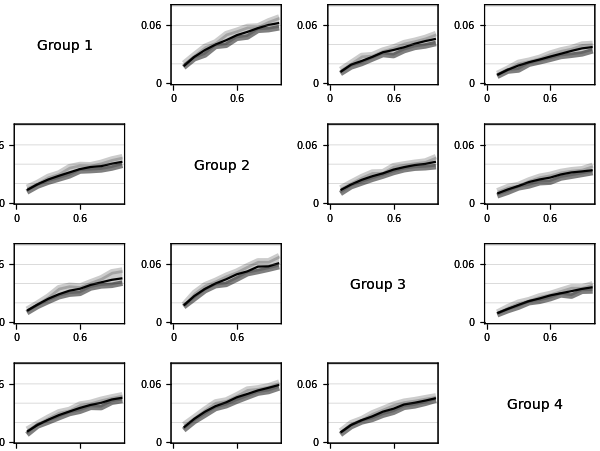

```mathematica
figreportingmeanswithuncertaintylabelled
```

# 4-age-class side-by-side grids

## 60/40 reporting with even transmission:

```mathematica
nensembles = 100;
RHigh = 1.5;
RLow =0.8;
NGMstruct = {
{1,1,1,1},
{1,1,1,1},
{1,1,1,1},
{1,1,1,1}
};

NGMHigh = RHigh*N[NGMstruct / Max[Eigenvalues[NGMstruct]]];
NGMLow = RLow*N[NGMstruct / Max[Eigenvalues[NGMstruct]]];
changepoint = 28; (*number of generation intervals after which to switch to the RLow*)
epilength = 175; (*length of epidemic in days*)
gensperbin = 2; (*number of generations per bin*)
genlength = 3.5; (*length of generation interval in days*)
noiserate =10; (*amount of noise to inject into each category, in each bin*)
nepidemics = 800; (*number of epidemics per STE calculation*)
minncases = 400;
ivecAllEnsembles = ConstantArray[{},nensembles];

SetSharedVariable[ivecAllEnsembles];
DistributeDefinitions[RHigh];
DistributeDefinitions[RLow];
DistributeDefinitions[NGMstruct];
DistributeDefinitions[NGMHigh];
DistributeDefinitions[NGMLow];
DistributeDefinitions[changepoint];
DistributeDefinitions[epilength];
DistributeDefinitions[gensperbin];
DistributeDefinitions[genlength];
DistributeDefinitions[noiserate];
DistributeDefinitions[nepidemics];
DistributeDefinitions[minncases];

ParallelDo[
ivecfull = {};
While[Length[ivecfull]< nepidemics,
initinf = {0,1,0,0}; (*the initial number infected in each class*)
If[Length[initinf]≠Length[NGMstruct], Print["ERROR: # initial conditions and # elements in NGM do not match"]; Return[]];
ivec = PoissonSim[initinf, genlength, epilength, changepoint, NGMHigh, NGMLow,gensperbin];
If[Total[Flatten[ivec]]>minncases, 
ivecnoisy = ivec +  RandomVariate[PoissonDistribution[noiserate], {Length[ivec],Length[NGMHigh]}];
ivecfull = Join[ivecfull, {ivecnoisy}]
];
];
ivecAllEnsembles⟦indexA⟧ = ivecfull;
,{indexA, nensembles}];
```

```mathematica
TEmatEqualTrans6040Reporting = ConstantArray[{},Length[ivecAllEnsembles]];
DistributeDefinitions[STEcalc];
DistributeDefinitions[ivecAllEnsembles];
SetSharedVariable[TEmatEqualTrans6040Reporting];
ParallelDo[
ivecfull = ivecAllEnsembles⟦indexB⟧;
nbands = Length[ivecfull⟦1,1⟧];
pvec = {.4, .6, .4, .4};
ivecfullReporting = Table[
Table[
Table[
RandomVariate[BinomialDistribution[ivecfull⟦loc,i,band⟧,pvec⟦band⟧]]
,{band,Length[ivecfull⟦loc,i⟧]}]
,{i,Length[ivecfull⟦loc⟧]}]
,{loc,Length[ivecfull]}];
TEmatEqualTrans6040Reporting⟦indexB⟧ = Table[Table[
If[i==j,0,STEcalc[ivecfullReporting⟦All,All,j⟧, ivecfullReporting⟦All,All,i⟧, 3]]
,{i,1,nbands}],{j,1,nbands}];
Print[indexB];
,{indexB, Length[ivecAllEnsembles]}]
```

```mathematica
Round[Mean[TEmatEqualTrans6040Reporting],0.001]//MatrixForm
```

(0. | 0.033 | 0.027 | 0.027
0.028 | 0. | 0.028 | 0.028
0.027 | 0.032 | 0. | 0.027
0.027 | 0.033 | 0.027 | 0.)

```mathematica
Round[Quantile[TEmatEqualTrans6040Reporting,0.025],0.001]//MatrixForm
```

(0. | 0.028 | 0.024 | 0.023
0.023 | 0. | 0.025 | 0.024
0.023 | 0.028 | 0. | 0.023
0.024 | 0.029 | 0.023 | 0.)

```mathematica
Round[Quantile[TEmatEqualTrans6040Reporting,0.975],0.001]//MatrixForm
```

(0. | 0.038 | 0.03 | 0.03
0.032 | 0. | 0.032 | 0.032
0.031 | 0.037 | 0. | 0.03
0.03 | 0.037 | 0.032 | 0.)

## 50/50 reporting with kids driving:

```mathematica
nensembles = 100;
RHigh = 1.5;
RLow =0.8;
NGMstruct = {
{1,2,1,1},
{1,4,1,1},
{1,2,1,1},
{1,1,1,1}
};
NGMHigh = RHigh*N[NGMstruct / Max[Eigenvalues[NGMstruct]]];
NGMLow = RLow*N[NGMstruct / Max[Eigenvalues[NGMstruct]]];
changepoint = 28; (*number of generation intervals after which to switch to the RLow*)
epilength = 175; (*length of epidemic in days*)
gensperbin = 2; (*number of generations per bin*)
genlength = 3.5; (*length of generation interval in days*)
noiserate =10; (*amount of noise to inject into each category, in each bin*)
nepidemics = 800; (*number of epidemics per STE calculation*)
minncases = 400;
ivecAllEnsembles = ConstantArray[{},nensembles];

SetSharedVariable[ivecAllEnsembles];
DistributeDefinitions[RHigh];
DistributeDefinitions[RLow];
DistributeDefinitions[NGMstruct];
DistributeDefinitions[NGMHigh];
DistributeDefinitions[NGMLow];
DistributeDefinitions[changepoint];
DistributeDefinitions[epilength];
DistributeDefinitions[gensperbin];
DistributeDefinitions[genlength];
DistributeDefinitions[noiserate];
DistributeDefinitions[nepidemics];
DistributeDefinitions[minncases];

ParallelDo[
ivecfull = {};
While[Length[ivecfull]< nepidemics,
initinf = {0,1,0,0}; (*the initial number infected in each class*)
If[Length[initinf]≠Length[NGMstruct], Print["ERROR: # initial conditions and # elements in NGM do not match"]; Return[]];
ivec = PoissonSim[initinf, genlength, epilength, changepoint, NGMHigh, NGMLow,gensperbin];
If[Total[Flatten[ivec]]>minncases, 
ivecnoisy = ivec +  RandomVariate[PoissonDistribution[noiserate], {Length[ivec],Length[NGMHigh]}];
ivecfull = Join[ivecfull, {ivecnoisy}]
];
];
ivecAllEnsembles⟦indexA⟧ = ivecfull;
,{indexA, nensembles}];
```

```mathematica
TEmatEqualTrans5050Reporting = ConstantArray[{},Length[ivecAllEnsembles]];
DistributeDefinitions[STEcalc];
DistributeDefinitions[ivecAllEnsembles];
SetSharedVariable[TEmatEqualTrans5050Reporting];
ParallelDo[
ivecfull = ivecAllEnsembles⟦indexB⟧;
nbands = Length[ivecfull⟦1,1⟧];
pvec = {.5, .5, .5, .5};
ivecfullReporting = Table[
Table[
Table[
RandomVariate[BinomialDistribution[ivecfull⟦loc,i,band⟧,pvec⟦band⟧]]
,{band,Length[ivecfull⟦loc,i⟧]}]
,{i,Length[ivecfull⟦loc⟧]}]
,{loc,Length[ivecfull]}];
TEmatEqualTrans5050Reporting⟦indexB⟧ = Table[Table[
If[i==j,0,STEcalc[ivecfullReporting⟦All,All,j⟧, ivecfullReporting⟦All,All,i⟧, 3]]
,{i,1,nbands}],{j,1,nbands}];
Print[indexB];
,{indexB, Length[ivecAllEnsembles]}]
```

```mathematica
Round[Mean[TEmatEqualTrans5050Reporting],0.001]//MatrixForm
```

(0. | 0.046 | 0.033 | 0.025
0.031 | 0. | 0.032 | 0.024
0.032 | 0.046 | 0. | 0.025
0.031 | 0.042 | 0.031 | 0.)

```mathematica
Round[Quantile[TEmatEqualTrans5050Reporting,0.025],0.001]//MatrixForm
```

(0. | 0.041 | 0.029 | 0.02
0.027 | 0. | 0.027 | 0.02
0.028 | 0.041 | 0. | 0.021
0.027 | 0.038 | 0.028 | 0.)

```mathematica
Round[Quantile[TEmatEqualTrans5050Reporting,0.975],0.001]//MatrixForm
```

(0. | 0.05 | 0.036 | 0.028
0.035 | 0. | 0.035 | 0.027
0.037 | 0.052 | 0. | 0.029
0.035 | 0.047 | 0.036 | 0.)

```mathematica
Mean[TEmatEqualTrans5050Reporting]
```

{{0,0.0460031,0.0325729,0.0245398},{0.0309093,0,0.0315691,0.0235986},{0.0321338,0.0459788,0,0.0245781},{0.0310727,0.0421549,0.0311291,0}}

# 12-age-class side-by-side grids

## 60/40 reporting with even transmission:

```mathematica
nensembles = 100;
RHigh = 1.5;
RLow =0.8;
NGMstruct = {
{1,1,1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1,1,1}
};

NGMHigh = RHigh*N[NGMstruct / Max[Eigenvalues[NGMstruct]]];
NGMLow = RLow*N[NGMstruct / Max[Eigenvalues[NGMstruct]]];
changepoint = 28; (*number of generation intervals after which to switch to the RLow*)
epilength = 175; (*length of epidemic in days*)
gensperbin = 2; (*number of generations per bin*)
genlength = 3.5; (*length of generation interval in days*)
noiserate =10; (*amount of noise to inject into each category, in each bin*)
nepidemics = 800; (*number of epidemics per STE calculation*)
minncases = 400;
ivecAllEnsembles = ConstantArray[{},nensembles];

SetSharedVariable[ivecAllEnsembles];
DistributeDefinitions[RHigh];
DistributeDefinitions[RLow];
DistributeDefinitions[NGMstruct];
DistributeDefinitions[NGMHigh];
DistributeDefinitions[NGMLow];
DistributeDefinitions[changepoint];
DistributeDefinitions[epilength];
DistributeDefinitions[gensperbin];
DistributeDefinitions[genlength];
DistributeDefinitions[noiserate];
DistributeDefinitions[nepidemics];
DistributeDefinitions[minncases];

ParallelDo[
ivecfull = {};
While[Length[ivecfull]< nepidemics,
insertspot = RandomInteger[{1,12}];
initinf = ConstantArray[0,12];
initinf⟦insertspot⟧ = 1;(*randomly insert the first infected into any one of the age bands*)
If[Length[initinf]≠Length[NGMstruct], Print["ERROR: # initial conditions and # elements in NGM do not match"]; Return[]];
ivec = PoissonSim[initinf, genlength, epilength, changepoint, NGMHigh, NGMLow,gensperbin];
If[Total[Flatten[ivec]]>minncases, 
ivecnoisy = ivec +  RandomVariate[PoissonDistribution[noiserate], {Length[ivec],Length[NGMHigh]}];
ivecfull = Join[ivecfull, {ivecnoisy}]
];
];
ivecAllEnsembles⟦indexA⟧ = ivecfull;
,{indexA, nensembles}];
```

```mathematica
Save["~/Dropbox (Harvard University)/Projects/STE/code/ivecAllEnsembles604012", ivecAllEnsembles];
```

```mathematica
Export["~/Desktop/started.txt", "Started at "<>DateString[]];
TEmatEqualTrans6040Reporting12 = ConstantArray[{},Length[ivecAllEnsembles]];
DistributeDefinitions[STEcalc];
DistributeDefinitions[ivecAllEnsembles];
SetSharedVariable[TEmatEqualTrans6040Reporting12];
ParallelDo[
ivecfull = ivecAllEnsembles⟦indexB⟧;
nbands = Length[ivecfull⟦1,1⟧];
pvec = {.6,.6,.6,.6,.6,.4, .4, .4,.4,.4,.4,.4};
ivecfullReporting12 = Table[
Table[
Table[
RandomVariate[BinomialDistribution[ivecfull⟦loc,i,band⟧,pvec⟦band⟧]]
,{band,Length[ivecfull⟦loc,i⟧]}]
,{i,Length[ivecfull⟦loc⟧]}]
,{loc,Length[ivecfull]}];
TEmatEqualTrans6040Reporting12⟦indexB⟧ = Table[Table[
If[i==j,0,STEcalc[ivecfullReporting12⟦All,All,j⟧, ivecfullReporting12⟦All,All,i⟧, 3]]
,{i,1,nbands}],{j,1,nbands}];
Print[indexB];
,{indexB, Length[ivecAllEnsembles]}]
Export["~/Desktop/finished.txt", "Finished at "<>DateString[]];
```

11

6

29

33

1

16

25

21

12

30

7

34

2

17

26

22

31

13

8

35

3

18

23

27

32

14

9

36

4

19

24

28

37

15

10

41

5

20

45

49

38

53

57

42

61

65

50

46

39

54

58

43

62

66

51

47

40

55

59

44

63

67

52

48

69

56

60

73

64

68

77

81

70

85

89

74

93

97

78

82

71

86

90

75

94

98

79

83

72

87

91

76

95

99

80

84

88

92

96

100

```mathematica
Save["~/Dropbox (Harvard University)/Projects/STE/code/TEmatEqualTrans6040Reporting12", TEmatEqualTrans6040Reporting12];
```

```mathematica
<<"~/Dropbox (Harvard University)/Projects/STE/code/TEmatEqualTrans6040Reporting12";
```

```mathematica
Dimensions[TEmatEqualTrans6040Reporting12]
```

{100,12,12}

```mathematica
Round[Mean[TEmatEqualTrans6040Reporting12],0.001]//MatrixForm
```

(0. | 0.008 | 0.008 | 0.008 | 0.008 | 0.007 | 0.007 | 0.006 | 0.006 | 0.007 | 0.007 | 0.007
0.008 | 0. | 0.008 | 0.008 | 0.008 | 0.007 | 0.006 | 0.007 | 0.007 | 0.007 | 0.006 | 0.006
0.008 | 0.008 | 0. | 0.008 | 0.008 | 0.006 | 0.007 | 0.007 | 0.006 | 0.007 | 0.007 | 0.006
0.008 | 0.008 | 0.008 | 0. | 0.008 | 0.007 | 0.007 | 0.006 | 0.007 | 0.007 | 0.007 | 0.006
0.008 | 0.008 | 0.008 | 0.008 | 0. | 0.007 | 0.007 | 0.007 | 0.007 | 0.006 | 0.006 | 0.007
0.007 | 0.007 | 0.007 | 0.007 | 0.007 | 0. | 0.006 | 0.006 | 0.006 | 0.006 | 0.006 | 0.006
0.007 | 0.007 | 0.007 | 0.007 | 0.007 | 0.006 | 0. | 0.006 | 0.006 | 0.006 | 0.006 | 0.006
0.007 | 0.007 | 0.007 | 0.007 | 0.007 | 0.006 | 0.006 | 0. | 0.006 | 0.006 | 0.006 | 0.006
0.007 | 0.007 | 0.007 | 0.007 | 0.007 | 0.006 | 0.006 | 0.006 | 0. | 0.006 | 0.006 | 0.006
0.007 | 0.007 | 0.007 | 0.007 | 0.007 | 0.006 | 0.006 | 0.006 | 0.006 | 0. | 0.006 | 0.006
0.007 | 0.007 | 0.007 | 0.007 | 0.007 | 0.006 | 0.006 | 0.006 | 0.006 | 0.006 | 0. | 0.006
0.007 | 0.007 | 0.007 | 0.007 | 0.007 | 0.006 | 0.006 | 0.006 | 0.006 | 0.006 | 0.006 | 0.)

```mathematica
Round[Quantile[TEmatEqualTrans6040Reporting12,0.025],0.001]//MatrixForm
```

(0. | 0.006 | 0.006 | 0.006 | 0.006 | 0.005 | 0.005 | 0.005 | 0.005 | 0.005 | 0.005 | 0.005
0.006 | 0. | 0.006 | 0.006 | 0.006 | 0.005 | 0.004 | 0.005 | 0.005 | 0.005 | 0.005 | 0.005
0.006 | 0.006 | 0. | 0.006 | 0.006 | 0.005 | 0.004 | 0.005 | 0.005 | 0.005 | 0.005 | 0.005
0.006 | 0.006 | 0.006 | 0. | 0.007 | 0.005 | 0.005 | 0.005 | 0.005 | 0.005 | 0.005 | 0.005
0.006 | 0.006 | 0.006 | 0.007 | 0. | 0.005 | 0.005 | 0.005 | 0.005 | 0.004 | 0.005 | 0.005
0.005 | 0.005 | 0.005 | 0.006 | 0.006 | 0. | 0.005 | 0.004 | 0.004 | 0.005 | 0.004 | 0.004
0.005 | 0.005 | 0.006 | 0.006 | 0.005 | 0.004 | 0. | 0.004 | 0.004 | 0.005 | 0.004 | 0.004
0.006 | 0.005 | 0.005 | 0.005 | 0.005 | 0.004 | 0.004 | 0. | 0.004 | 0.004 | 0.004 | 0.004
0.006 | 0.005 | 0.006 | 0.005 | 0.005 | 0.004 | 0.004 | 0.004 | 0. | 0.004 | 0.004 | 0.004
0.006 | 0.005 | 0.006 | 0.005 | 0.005 | 0.004 | 0.004 | 0.004 | 0.005 | 0. | 0.004 | 0.004
0.005 | 0.005 | 0.005 | 0.005 | 0.005 | 0.004 | 0.004 | 0.004 | 0.004 | 0.004 | 0. | 0.004
0.005 | 0.005 | 0.005 | 0.005 | 0.005 | 0.004 | 0.004 | 0.004 | 0.004 | 0.004 | 0.004 | 0.)

```mathematica
Round[Quantile[TEmatEqualTrans6040Reporting12,0.975],0.001]//MatrixForm
```

(0. | 0.011 | 0.01 | 0.01 | 0.01 | 0.008 | 0.009 | 0.008 | 0.009 | 0.009 | 0.009 | 0.009
0.01 | 0. | 0.011 | 0.011 | 0.01 | 0.009 | 0.009 | 0.009 | 0.009 | 0.009 | 0.009 | 0.009
0.01 | 0.01 | 0. | 0.011 | 0.01 | 0.008 | 0.008 | 0.009 | 0.008 | 0.009 | 0.008 | 0.009
0.01 | 0.01 | 0.01 | 0. | 0.01 | 0.009 | 0.008 | 0.008 | 0.009 | 0.009 | 0.009 | 0.008
0.01 | 0.011 | 0.011 | 0.011 | 0. | 0.008 | 0.009 | 0.008 | 0.009 | 0.009 | 0.008 | 0.009
0.009 | 0.009 | 0.009 | 0.01 | 0.009 | 0. | 0.008 | 0.008 | 0.008 | 0.007 | 0.007 | 0.007
0.009 | 0.009 | 0.009 | 0.01 | 0.009 | 0.008 | 0. | 0.008 | 0.008 | 0.008 | 0.008 | 0.008
0.009 | 0.01 | 0.009 | 0.009 | 0.009 | 0.008 | 0.008 | 0. | 0.008 | 0.008 | 0.008 | 0.007
0.01 | 0.01 | 0.01 | 0.009 | 0.009 | 0.008 | 0.007 | 0.008 | 0. | 0.007 | 0.008 | 0.008
0.009 | 0.009 | 0.009 | 0.009 | 0.01 | 0.007 | 0.007 | 0.007 | 0.008 | 0. | 0.008 | 0.007
0.009 | 0.009 | 0.009 | 0.01 | 0.009 | 0.007 | 0.008 | 0.007 | 0.007 | 0.008 | 0. | 0.008
0.009 | 0.009 | 0.01 | 0.009 | 0.009 | 0.008 | 0.008 | 0.008 | 0.008 | 0.008 | 0.007 | 0.)

## 50/50 reporting with kids driving:

```mathematica
nensembles = 100;
RHigh = 1.5;
RLow =0.8;
NGMstruct = {
{1,1,2,2,2,1,1,1,1,1,1,1},
{1,1,2,2,2,1,1,1,1,1,1,1},
{1,1,4,4,4,1,1,1,1,1,1,1},
{1,1,4,4,4,1,1,1,1,1,1,1},
{1,1,4,4,4,1,1,1,1,1,1,1},
{1,1,2,2,2,1,1,1,1,1,1,1},
{1,1,2,2,2,1,1,1,1,1,1,1},
{1,1,2,2,2,1,1,1,1,1,1,1},
{1,1,2,2,2,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1,1,1}
};
NGMHigh = RHigh*N[NGMstruct / Max[Eigenvalues[NGMstruct]]];
NGMLow = RLow*N[NGMstruct / Max[Eigenvalues[NGMstruct]]];
changepoint = 28; (*number of generation intervals after which to switch to the RLow*)
epilength = 175; (*length of epidemic in days*)
gensperbin = 2; (*number of generations per bin*)
genlength = 3.5; (*length of generation interval in days*)
noiserate =10; (*amount of noise to inject into each category, in each bin*)
nepidemics = 800; (*number of epidemics per STE calculation*)
minncases = 400;
ivecAllEnsembles = ConstantArray[{},nensembles];

SetSharedVariable[ivecAllEnsembles];
DistributeDefinitions[RHigh];
DistributeDefinitions[RLow];
DistributeDefinitions[NGMstruct];
DistributeDefinitions[NGMHigh];
DistributeDefinitions[NGMLow];
DistributeDefinitions[changepoint];
DistributeDefinitions[epilength];
DistributeDefinitions[gensperbin];
DistributeDefinitions[genlength];
DistributeDefinitions[noiserate];
DistributeDefinitions[nepidemics];
DistributeDefinitions[minncases];

ParallelDo[
ivecfull = {};
While[Length[ivecfull]< nepidemics,
insertspot = RandomInteger[{1,12}];
initinf = ConstantArray[0,12];
initinf⟦insertspot⟧ = 1;
If[Length[initinf]≠Length[NGMstruct], Print["ERROR: # initial conditions and # elements in NGM do not match"]; Return[]];
ivec = PoissonSim[initinf, genlength, epilength, changepoint, NGMHigh, NGMLow,gensperbin];
If[Total[Flatten[ivec]]>minncases, 
ivecnoisy = ivec +  RandomVariate[PoissonDistribution[noiserate], {Length[ivec],Length[NGMHigh]}];
ivecfull = Join[ivecfull, {ivecnoisy}]
];
];
ivecAllEnsembles⟦indexA⟧ = ivecfull;
,{indexA, nensembles}];
```

```mathematica
TEmatEqualTrans5050Reporting12 = ConstantArray[{},Length[ivecAllEnsembles]];
DistributeDefinitions[STEcalc];
DistributeDefinitions[ivecAllEnsembles];
SetSharedVariable[TEmatEqualTrans5050Reporting12];
ParallelDo[
ivecfull = ivecAllEnsembles⟦indexB⟧;
nbands = Length[ivecfull⟦1,1⟧];
pvec = ConstantArray[.5,12];
ivecfullReporting12 = Table[
Table[
Table[
RandomVariate[BinomialDistribution[ivecfull⟦loc,i,band⟧,pvec⟦band⟧]]
,{band,Length[ivecfull⟦loc,i⟧]}]
,{i,Length[ivecfull⟦loc⟧]}]
,{loc,Length[ivecfull]}];
TEmatEqualTrans5050Reporting12⟦indexB⟧ = Table[Table[
If[i==j,0,STEcalc[ivecfullReporting12⟦All,All,j⟧, ivecfullReporting12⟦All,All,i⟧, 3]]
,{i,1,nbands}],{j,1,nbands}];
Print[indexB];
,{indexB, Length[ivecAllEnsembles]}]
```

21

1

29

6

25

11

33

16

22

30

2

26

7

34

12

17

23

31

3

35

8

27

13

18

24

32

4

36

28

9

14

19

37

41

5

45

49

10

15

20

38

42

46

53

50

57

61

65

39

43

47

54

51

58

62

66

40

44

48

55

52

59

63

67

69

73

77

56

81

60

64

68

70

74

78

82

85

89

93

97

71

75

79

83

86

90

94

98

72

76

80

84

87

91

95

99

88

92

96

100

```mathematica
Round[Mean[TEmatEqualTrans5050Reporting12],0.001]//MatrixForm
```

(0. | 0.008 | 0.012 | 0.011 | 0.011 | 0.007 | 0.007 | 0.008 | 0.008 | 0.006 | 0.006 | 0.006
0.008 | 0. | 0.012 | 0.011 | 0.011 | 0.008 | 0.007 | 0.007 | 0.007 | 0.006 | 0.005 | 0.006
0.009 | 0.009 | 0. | 0.014 | 0.014 | 0.009 | 0.009 | 0.008 | 0.009 | 0.006 | 0.006 | 0.006
0.008 | 0.009 | 0.014 | 0. | 0.014 | 0.008 | 0.009 | 0.009 | 0.009 | 0.006 | 0.006 | 0.006
0.009 | 0.009 | 0.014 | 0.014 | 0. | 0.009 | 0.008 | 0.009 | 0.008 | 0.006 | 0.006 | 0.006
0.007 | 0.007 | 0.011 | 0.012 | 0.011 | 0. | 0.007 | 0.007 | 0.007 | 0.006 | 0.006 | 0.006
0.007 | 0.008 | 0.011 | 0.012 | 0.012 | 0.008 | 0. | 0.008 | 0.007 | 0.005 | 0.005 | 0.006
0.007 | 0.007 | 0.011 | 0.012 | 0.011 | 0.007 | 0.008 | 0. | 0.007 | 0.006 | 0.006 | 0.005
0.008 | 0.007 | 0.012 | 0.012 | 0.012 | 0.008 | 0.008 | 0.007 | 0. | 0.006 | 0.006 | 0.006
0.006 | 0.006 | 0.009 | 0.009 | 0.009 | 0.006 | 0.006 | 0.006 | 0.006 | 0. | 0.005 | 0.005
0.006 | 0.006 | 0.009 | 0.009 | 0.009 | 0.006 | 0.006 | 0.006 | 0.006 | 0.005 | 0. | 0.005
0.006 | 0.006 | 0.009 | 0.009 | 0.009 | 0.006 | 0.006 | 0.006 | 0.006 | 0.005 | 0.005 | 0.)

```mathematica
Round[Quantile[TEmatEqualTrans5050Reporting12,0.025],0.001]//MatrixForm
```

(0. | 0.006 | 0.009 | 0.009 | 0.008 | 0.006 | 0.005 | 0.005 | 0.006 | 0.004 | 0.004 | 0.004
0.006 | 0. | 0.009 | 0.009 | 0.009 | 0.005 | 0.006 | 0.005 | 0.006 | 0.004 | 0.004 | 0.004
0.007 | 0.007 | 0. | 0.012 | 0.011 | 0.007 | 0.007 | 0.007 | 0.007 | 0.005 | 0.005 | 0.005
0.006 | 0.007 | 0.011 | 0. | 0.011 | 0.006 | 0.007 | 0.007 | 0.007 | 0.005 | 0.004 | 0.005
0.007 | 0.007 | 0.012 | 0.011 | 0. | 0.007 | 0.006 | 0.006 | 0.006 | 0.005 | 0.005 | 0.005
0.005 | 0.005 | 0.009 | 0.009 | 0.009 | 0. | 0.006 | 0.005 | 0.005 | 0.004 | 0.004 | 0.004
0.005 | 0.006 | 0.009 | 0.009 | 0.009 | 0.006 | 0. | 0.006 | 0.005 | 0.004 | 0.004 | 0.004
0.005 | 0.006 | 0.009 | 0.009 | 0.009 | 0.005 | 0.006 | 0. | 0.005 | 0.004 | 0.004 | 0.004
0.006 | 0.006 | 0.009 | 0.008 | 0.009 | 0.006 | 0.006 | 0.006 | 0. | 0.004 | 0.004 | 0.004
0.005 | 0.005 | 0.007 | 0.007 | 0.007 | 0.005 | 0.005 | 0.005 | 0.005 | 0. | 0.004 | 0.003
0.005 | 0.005 | 0.007 | 0.007 | 0.007 | 0.004 | 0.005 | 0.005 | 0.004 | 0.003 | 0. | 0.003
0.004 | 0.005 | 0.007 | 0.007 | 0.007 | 0.005 | 0.005 | 0.004 | 0.004 | 0.004 | 0.003 | 0.)

```mathematica
Round[Quantile[TEmatEqualTrans5050Reporting12,0.975],0.001]//MatrixForm
```

(0. | 0.01 | 0.014 | 0.014 | 0.014 | 0.01 | 0.01 | 0.009 | 0.01 | 0.007 | 0.007 | 0.007
0.011 | 0. | 0.014 | 0.015 | 0.014 | 0.01 | 0.01 | 0.01 | 0.009 | 0.007 | 0.007 | 0.007
0.011 | 0.011 | 0. | 0.017 | 0.016 | 0.011 | 0.011 | 0.011 | 0.011 | 0.008 | 0.008 | 0.008
0.011 | 0.011 | 0.016 | 0. | 0.016 | 0.011 | 0.011 | 0.011 | 0.011 | 0.008 | 0.009 | 0.008
0.011 | 0.011 | 0.016 | 0.017 | 0. | 0.011 | 0.01 | 0.011 | 0.011 | 0.008 | 0.008 | 0.008
0.009 | 0.01 | 0.014 | 0.015 | 0.014 | 0. | 0.009 | 0.01 | 0.009 | 0.007 | 0.007 | 0.007
0.01 | 0.01 | 0.014 | 0.014 | 0.015 | 0.01 | 0. | 0.01 | 0.009 | 0.007 | 0.007 | 0.007
0.01 | 0.01 | 0.013 | 0.014 | 0.014 | 0.01 | 0.011 | 0. | 0.009 | 0.007 | 0.007 | 0.007
0.01 | 0.01 | 0.014 | 0.015 | 0.015 | 0.01 | 0.009 | 0.01 | 0. | 0.007 | 0.007 | 0.008
0.008 | 0.009 | 0.012 | 0.011 | 0.011 | 0.009 | 0.008 | 0.008 | 0.008 | 0. | 0.007 | 0.007
0.008 | 0.008 | 0.011 | 0.011 | 0.011 | 0.008 | 0.008 | 0.008 | 0.008 | 0.006 | 0. | 0.006
0.008 | 0.008 | 0.012 | 0.012 | 0.012 | 0.008 | 0.008 | 0.008 | 0.008 | 0.006 | 0.006 | 0.)

```mathematica
Mean[TEmatEqualTrans5050Reporting12]
```

{{0,0.00754296,0.0116,0.011346,0.0113051,0.0074887,0.00739382,0.00751019,0.0075309,0.00562998,0.00555843,0.00570251},{0.0076646,0,0.0115259,0.0114416,0.0113576,0.00753643,0.00749924,0.0074485,0.00741273,0.00560458,0.00548828,0.00563367},{0.00858573,0.0085825,0,0.0141182,0.0138839,0.00867512,0.00874128,0.00849903,0.00861157,0.00639438,0.00627851,0.00631673},{0.00849807,0.00851772,0.0138033,0,0.0139143,0.00848018,0.00855301,0.00867125,0.00862555,0.00628078,0.00631713,0.00628505},{0.00863091,0.00879742,0.0140096,0.0139218,0,0.00867337,0.00846121,0.00855284,0.00840815,0.00646965,0.0063397,0.0063041},{0.00731203,0.00742865,0.0114819,0.0116263,0.0114881,0,0.00745826,0.00733107,0.00717245,0.00555163,0.00553206,0.00566454},{0.00726591,0.00750353,0.0114979,0.011563,0.0115693,0.00753223,0,0.00756684,0.00728545,0.00547724,0.00541931,0.00571219},{0.00741936,0.00747356,0.0114287,0.0115134,0.0114367,0.00739439,0.00763825,0,0.00735421,0.00552198,0.00551893,0.00542576},{0.00766661,0.00738045,0.0115793,0.0115994,0.0116594,0.00752676,0.0075351,0.00739664,0,0.00566694,0.0056299,0.00559623},{0.00619254,0.00631825,0.00908183,0.00895436,0.00905753,0.00641859,0.00627341,0.00628956,0.00620595,0,0.00498268,0.00485943},{0.00622725,0.00632748,0.00888157,0.00909358,0.00901198,0.00616353,0.00642286,0.0064242,0.00626047,0.00479953,0,0.00473456},{0.00609688,0.00619423,0.00896681,0.0088669,0.00899332,0.00620892,0.00612373,0.00614598,0.00621209,0.00481591,0.00482685,0}}

# Real STE grid:

```mathematica
pairwiseTEs2009 = Import["/Users/sk792/DropboxHarvard/Projects/STE/Interface/Submission1/data/pairwiseTEs2009.csv"];
```

```mathematica
ageclasses= {"<2","2-4","5-9","10-14","15-19","20-29","30-39","40-49","50-59","60-69","70-79","80+"};
```

```mathematica
titlefs = 14;
labelfs= 12;
```

```mathematica
subtractval = Min[DeleteCases[Flatten[pairwiseTEs2009],_?(#==0&)]]
```

0.005603

```mathematica
xshift = 0.2;
```

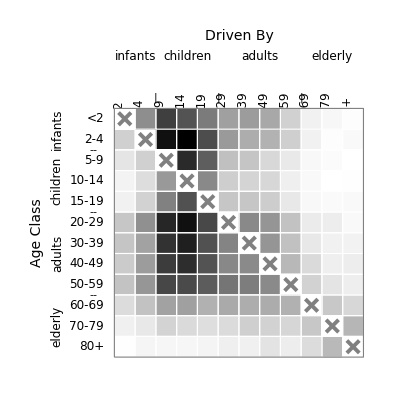

```mathematica
figteboxes2009 = Graphics[
{Text[Rotate[Style["Age Class",FontSize->titlefs],90 Degree],{-2.75,7}],Text[Style["Driven By",FontSize->titlefs],{7,16.5}],
Text[Style["infants",FontSize->labelfs],{2,15.5}],
Text[Style["children",FontSize->labelfs],{4.5,15.5}],
Text[Style["adults",FontSize->labelfs],{8,15.5}],
Text[Style["elderly",FontSize->labelfs],{11.5,15.5}],
Text[Rotate[Style["infants",FontSize->labelfs],90 Degree],{-1.75,12}],
Text[Rotate[Style["children",FontSize->labelfs],90 Degree],{-1.75,9.5}],
Text[Rotate[Style["adults",FontSize->labelfs],90 Degree],{-1.75,6}],
Text[Rotate[Style["elderly",FontSize->labelfs],90 Degree],{-1.75,2.5}],
Text["|", {3,13.5}],Text["|", {6,13.5}],Text["|", {10,13.5}],
Text["--", {0,4}],Text["--", {0,8}],Text["--", {0,11}],

Table[Text[Rotate[Style[ageclasses⟦i⟧,FontSize->labelfs],90Degree,{Left,Center}],{i+.5,13},{0,-1}],{i,1,12}],
Table[Text[Style[ageclasses⟦i⟧,FontSize->labelfs],{.5,13-(i-.5)},{1,0}],{i,1,12}],

Table[Table[{GrayLevel[1-(pairwiseTEs2009⟦i,j⟧-subtractval)/(Max[pairwiseTEs2009]-subtractval)],Rectangle[{j,13-i}]},{i,1,12}],{j,1,12}],
Opacity[0], EdgeForm[{White,Opacity[1]}],
Table[Table[{Rectangle[{j,13-i}]},{i,1,12}],{j,1,12}],
EdgeForm[{Gray,Opacity[1]}],
Rectangle[{1,1},{13,13}],

Gray, Opacity[1],Thickness[0.007],
Table[Line[{{1+xshift+i,12+xshift-i},{2-xshift+i,13-xshift-i}}],{i,0,11}],
Table[Line[{{1+xshift+i,13-xshift-i},{2-xshift+i,12+xshift-i}}],{i,0,11}]
}, ImagePadding->10]
```